```mathematica
numberOfAgents = 10;
donationCost = -10;
buyCost = -200;
poolBuyCost=-150;
usageUtil = 5;
waitUtil = -1;

agentParams = Array[Function[x,
{(*RandomReal[0.4], (* How often a tool is needed *)*)
0.4,
RandomReal[0.02], (* Prob to buy tool *)
RandomReal[0.05], (* Prob to donate *)
0 (* Has tool (tool health) *)
}],numberOfAgents];
```

```mathematica
(* Returns the utility, the updated agent, and change in poolHealth.
int, agent, int *)
CalculatePayoff[agent_,nPTools_]:=Module[
{p=agent[[1]],pb=agent[[2]],
pd=agent[[3]],toolHealth=agent[[4]],
util=0,poolHealthChange=0},
If[RandomReal[]<p,
If[toolHealth>0,
util=usageUtil; toolHealth-=1,
If[RandomReal[]<pb,
toolHealth=10;
util=buyCost+usageUtil,
If[nPTools>0,
util=usageUtil;poolHealthChange-=1,
util=waitUtil]
]
],
If[RandomReal[]<pd,
poolHealthChange+=5;
util=donationCost,
util=0
]
];
{util,{p,pb,pd,toolHealth},poolHealthChange}
];

CalculatePayoff[{0,0,1,5},3]
```

{-10,{0,0,1,5},5}

```mathematica
MutateAgent[vv_] := Module[{v=vv},
If[v>0.5,distance = 1-v,distance =v];
value:=RandomVariate[NormalDistribution[v,(distance/4)+0.1]];
Print[value];
Return[If[value<=0,0,Min[value,1]]];
];
MutateAgent[0]
```

0.0312611

0

{14,-126,-257,7,-135,-317,6,10,13,0}

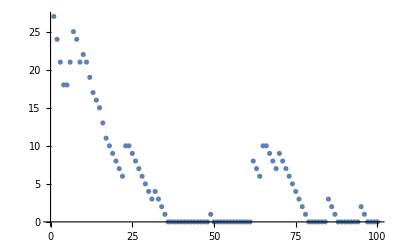

```mathematica
DoRound[agentList_,initPoolHealth_,iterations_]:=Module[
{fullTool=10,
poolHealth=initPoolHealth,
agents=agentList,
agentPayoffs=ConstantArray[0,Length[agentList]],
PHhistory = {}},
For[i=0,i<iterations,i++,
nPoolTools=poolHealth/fullTool;
For[j=1,j<Length[agents],j++,
{payoff, newAgent, healthChange}=CalculatePayoff[agents[[j]],nPoolTools];
agentPayoffs[[j]]+=payoff;
agents[[j]]=newAgent;
poolHealth+=healthChange;
nPoolTools +=healthChange;
];
PHhistory = Append[PHhistory,poolHealth];
];
{agentPayoffs, PHhistory}
];

{po, hp} =DoRound[agentParams,30,100];
po
ListPlot[hp]
```